```mathematica
Manipulate[{Range[n],Range[m,n],Range[m,n,d]},{n,0,9},{m,0,9},{d,0,9}]
(* m起始点 n终止点 d步长 *)
```

```mathematica
Range[{3,4}](*生成两张表*)
```

{{1,2,3},{1,2,3,4}}

Table::iterb: 迭代器 {k,m,n,d} 没有适当的边界.

Table[expr,{k,m,n,d}]

{x_1,x_2,x_3,x_4,x_5,x_6,x_7,x_8,x_9,x_10}

{x_1^3,x_2^3,x_3^3,x_4^3,x_5^3,x_6^3,x_7^3,x_8^3,x_9^3,x_10^3}

(11 | 12 | 13 | 14
21 | 22 | 23 | 24
31 | 32 | 33 | 34)

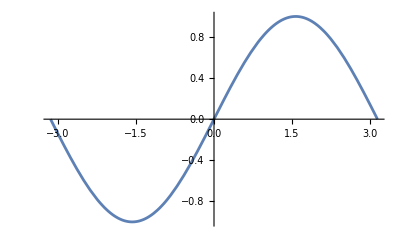
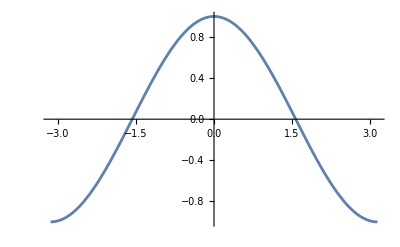
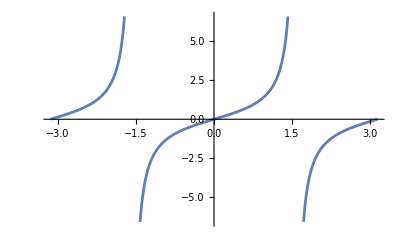
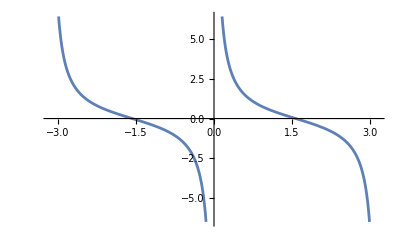

```mathematica
Table[expr,{k,m,n,d}](*exper可为函数或者量等，k为变量，步长和初始值为1时可省略*)(*创建表格*)
X=Table[Subscript[x, i],{i,10}]
X^3(*表示每个元素进行三次方运算*)
B=Table[10 i+j,{i,3},{j,4}](*i为行数，j为列数*)
Table[Plot[f[x],{x,-Pi,Pi}],{f,{Sin,Cos,Tan,Cot}}](*甚至可用于画图*)
```

```mathematica
(*随机表*)
ClearAll
RandomInteger[]
RandomReal[]
range={1,2}
RandomReal[range,2]
```

ClearAll

0

0.856455

{1,2}

{1.23934,1.36895}

```mathematica
(*递归表*)
RecurrenceTable[{f[n]==f[n-1]+f[n-2],f[1]==1,f[2]==1},f,{n,8}](*f为递归函数，n为递归变量*)
Table[Fibonacci[n],{n,8}]
```

{1,1,2,3,5,8,13,21}

{1,1,2,3,5,8,13,21}

```mathematica
(*元素表示*)
ClearAll
B=Table[Subscript[b, i,j],{i,3},{j,3}]
B[[1]](*B的第一行元素*)
B[[1,1]](*B的第一行元素的第一个*)
B[1](*B的第一个元素  *)
(*与C语言中数组类似*)
TableForm[B]
(*Subscript[可以直接对b, i,j] 赋值或对使用上述列表元素的表示法对列表赋值*)
(*Subscript[b, ij] 这样写的话ij变成一个变量了，还是得加，哭*)
```

ClearAll

{{b_(1,1),b_(1,2),b_(1,3)},{b_(2,1),b_(2,2),b_(2,3)},{b_(3,1),b_(3,2),b_(3,3)}}

{b_(1,1),b_(1,2),b_(1,3)}

b_(1,1)

{{b_(1,1),b_(1,2),b_(1,3)},{b_(2,1),b_(2,2),b_(2,3)},{b_(3,1),b_(3,2),b_(3,3)}}[1]

b_(1,1) | b_(1,2) | b_(1,3)
b_(2,1) | b_(2,2) | b_(2,3)
b_(3,1) | b_(3,2) | b_(3,3)